## Constants

```mathematica
SetDirectory["/Users/shainen/Dropbox/Research/bhsucon/nb/nb/"];
```

```mathematica
Get["constants.m"]
```

```mathematica
TE=32;
```

## Get QM

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/siteone";
```

```mathematica
QMSz=Import["data/QMAvgSz","Table"];
```

```mathematica
QMwid=Import["data/QMWidSz","Table"];
```

```mathematica
Dimensions[QMSz]
```

{3,128}

```mathematica
QM=ListPlot[Table[{times[[1;;TE]],QMSz[[n,1;;TE]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted];
```

```mathematica
QMw=ListPlot[Table[{times,QMwid[[n]]}ᵀ,{n,1,3}],Joined->True];
```

## Get Wig SU3

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/ht";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su3dw6uj10010t";
```

```mathematica
<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su3dw6uj100ht";
```

```mathematica
Get[su3outfile<>"a"];
```

```mathematica
Get["data/su3S3t200j0.01r1000.lsta"];
```

```mathematica
su3outfile
```

data/su3S3t200j0.01r100.lst

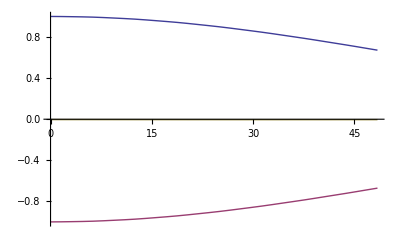

```mathematica
TWAsu3=ListPlot[Table[{times[[1;;TE]],2avgspins3[[1;;TE,1,n,3]]}ᵀ,{n,1,3}],Joined->True]
```

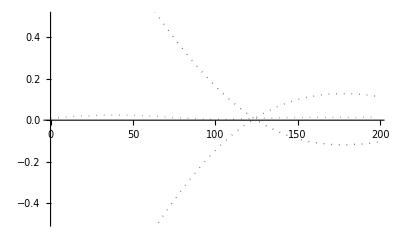

```mathematica
TWAsu3o=ListPlot[Table[{times,2avgspins3[[All,1,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted]
```

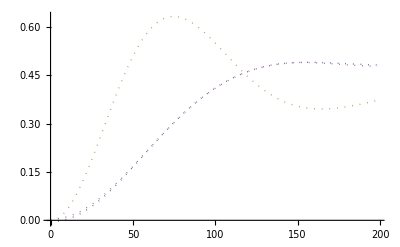

```mathematica
TWAsu3w=ListPlot[Table[{times,4avgspins3[[All,2,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted]
```

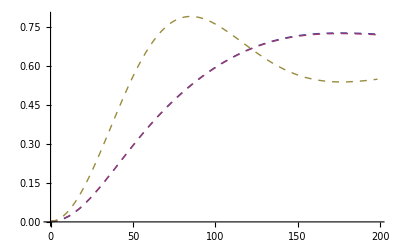

```mathematica
TWAsu3w8=ListPlot[Table[{times,2/3(1-√3 avgspins3[[All,1,n,8]])-4 avgspins3[[All,1,n,3]]^2}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dashed]
```

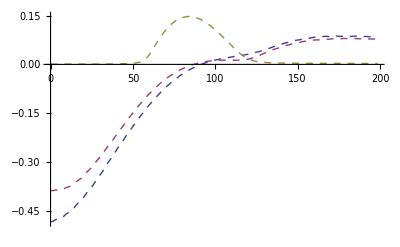

```mathematica
TWAsu3w8oc=ListPlot[Table[{times,2/3(√Sum[avgspins3[[All,1,n,m]]^2,{m,1,8}]-avgspins3[[All,1,n,8]])-4 avgspins3[[All,1,n,3]]^2}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dashed]
```

## Get Wig SU2

```mathematica
(*<<"/Users/shainen/Dropbox/Research/bhsucon/su2dw6ht";*)
```

```mathematica
(*<<"/Users/shainen/Dropbox/Research/bhsucon/sofarsu2";*)
```

```mathematica
(*<<"/Users/shainen/Dropbox/Research/bhsucon/nb/nb/su2dw6uj1001m";*)
```

```mathematica
(*avgspins2=%;*)
```

```mathematica
Get[su2outfile];
```

```mathematica
su2outfile
```

```mathematica
Get["data/su2S3t200j0.01r10000.lst"];
```

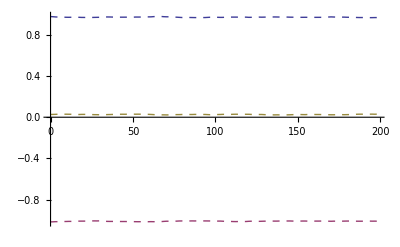

```mathematica
TWAsu2=ListPlot[Table[{times,avgspins2[[All,1,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dashed]
```

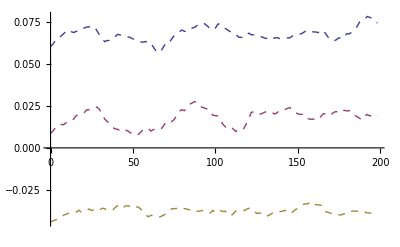

```mathematica
TWAsu2w=ListPlot[Table[{times,avgspins2[[All,2,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dashed]
```

## Plots

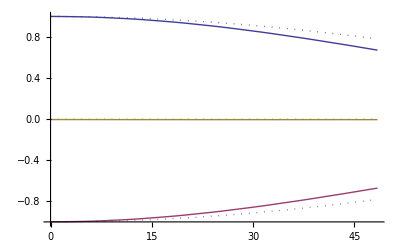

```mathematica
Show[TWAsu3,QM,PlotRange->{-1,1},AxesOrigin->{0,-1}]
```

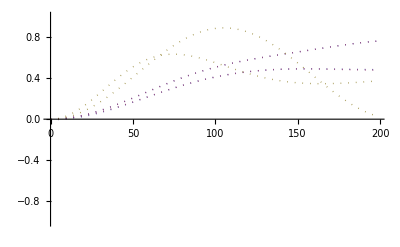

```mathematica
Show[TWAsu3w,QMw,PlotRange->{-1,1},AxesOrigin->{0,0}]
```

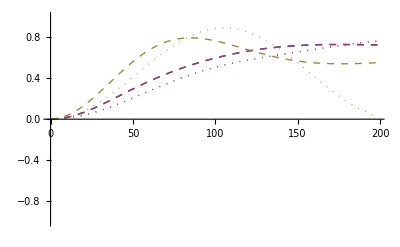

```mathematica
Show[TWAsu3w8,QMw,PlotRange->{-1,1},AxesOrigin->{0,0}]
```

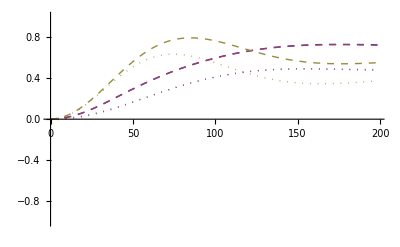

```mathematica
Show[TWAsu3w8,TWAsu3w,PlotRange->{-1,1},AxesOrigin->{0,0}]
```